# CASO 1I

```mathematica
<< "D:\Users\jontx\Dropbox\Clase\2 Master\RRT\Caso 2\drawTx.m"
<<"D:\Users\jontx\Dropbox\Clase\2 Master\RRT\Caso 2\RandomData.m"
```

```mathematica
?drawTx`*
```

```mathematica
?RandomData`*
```

## Parte 0: Primeros pasos y cola M/M/1

1. Estudiar la librería de representación de paquetes que se proporciona para identificar como se definen los parámetros de la transmisión y que formato deben tener los paquetes que se proporcionan para la representación.

Antes de usar la librería tenemos que inicializarla con SetIniParDraw. Esta funcion recibe como parametros el tiempo de propagación y el ts.

Despues usamos DrawWin para dibujar el marco de tiempo y DrawPacket para dibujar los paquetes. 

DrawWin toma como parametros el tiempo de inicio, el tiempo total que se va a dibujar y el módulo que se utilizará para numerar las secuencias. Por otro lado, DrawPacket toma como parametro una variable con el siguiente formato: { tiempo de inserción, tasa de servicio , número secuencia, error transmisión, número de repeticiones}.

OJO!!!. La tasa de servicio debe ser multiplo de 9600 ya que, por como esta hecha la librería, un segundo equivale a 9600.

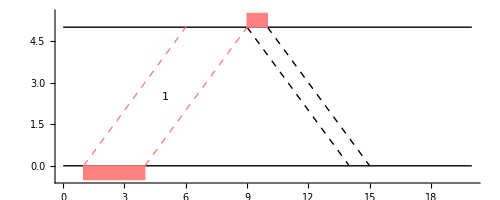

```mathematica
packet={1,9600*3,1,0,0}; 
SetIniParDraw[5,1];
Show[DrawWin[0,20,8],DrawPacketTx[packet]]
```

```mathematica
packetList=Table[{2+n*10,9600,n+1,0,0},{n,0,9}];
Manipulate[Show[DrawWin[origin,ww,8],Map[DrawPacketTx[#]&,packetList]],{origin,0,100-ww},{ww,10,50}]
```

En el caso 1 hemos hecho unas funciones que trabajan con el tiempo de llegada y con el tiempo de salida. Sin embargo, para genererar los paquetes nos hace falta calcular el tiempo de inserción. Ello se consigue restandole al tiempo de salida el tiempo de servicio.

2. Probar la representación de la librería para una cola M/M/1.

```mathematica
FifoSchedulling[arrivalsTime_,serviceTime_]:=
Module[{n,checkTime},n=1;checkTime=arrivalsTime[[1]];
Map[(If[checkTime≥#,checkTime+=serviceTime[[n++]],checkTime=#+serviceTime[[n++]]])&,arrivalsTime]]


CalculateMM1Packets[insertionTime_, serviceTime_]:=
Module[{n},
n=0;
Map[ 
({#, 9600*serviceTime[[n+1]],n++, 0, 0})&, insertionTime]
]

SimTxMM1[lamdaMM1_,muMM1_,nPacketsMM1_,tpropMM1_,tsMM1_]:=Module[

{arrivalsTimeMM1, serviceTimeMM1,departureTimeMM1,insertionTimeMM1,  packetsMM1},
(
arrivalsTimeMM1=Accumulate[Table[RandomExp[lamdaMM1],nPacketsMM1]];
serviceTimeMM1=Table[RandomExp[muMM1], nPacketsMM1];
SetIniParDraw[tpropMM1,tsMM1];
departureTimeMM1=FifoSchedulling[arrivalsTimeMM1, serviceTimeMM1];
insertionTimeMM1=departureTimeMM1-serviceTimeMM1;
packetsMM1=CalculateMM1Packets[insertionTimeMM1, serviceTimeMM1];
Return[packetsMM1]
)]
```

```mathematica
muMM1=100;
lamdaMM1=80;
nPacketsMM1=1000;
tpropMM1=0.05;
tsMM1=0.005;

packetsMM1=SimTxMM1[lamdaMM1,muMM1,nPacketsMM1,tpropMM1,tsMM1];
SetIniParDraw[tpropMM1,tsMM1];
Manipulate[Show[DrawWin[origin,ww,8],Map[DrawPacketTx[#]&,packetsMM1]],{origin,packetsMM1[[1]][[1]]-0.0001,packetsMM1[[-1]][[1]]+2*tpropMM1+tsMM1-ww},{ww,0.1,1}]
```

Tal y como se puede observar, la simulacion cumple con el funcionamiento de una cola M/M/1. Los paquetes que llegan salen nada mas haya hueco en la cola.

## Parte I: Stop & Wait

Stop & Wait consiste en que un paquete no se envie hasta recibir la confirmación de que el paquete anterior ha llegado correctamente. Es decir, el tiempo de espera de un paquete a otro viene dado por el tiempo de servicio mas 2 veces el tiempo de propagación mas el tiempo que se tarda en procesar y generar el ACK en el receptor.

Por otro lado, si un paquete no recibe confirmación, este se reenviará hasta que llegue correctamente, y los demás paquetes deberán esperar.

```mathematica
StopAndWait[arrivalsTime_, serviceTime_,tprop_, ts_, prob_, nPacketsTotal_]:=
Module[{i,nSec, insertionTime, packetList},
i=1;
nSec=0;
insertionTime=0;
packetList={};
Map[
(
If[# > insertionTime, insertionTime=#; ];
While[RandomReal[] < prob && Length[packetList]< nPacketsTotal,
AppendTo[packetList, {insertionTime,9600* serviceTime[[i]],nSec,1,0}];

insertionTime+=(serviceTime[[i]]+2*tprop+ts);];

If[Length[packetList]< nPacketsTotal,
AppendTo[packetList, {insertionTime,9600* serviceTime[[i]],nSec++,0,0}];

insertionTime+=(serviceTime[[i++]]+2*tprop+ts); 
];

)&,arrivalsTime];
Return[packetList]
]
```

```mathematica
SimTxSW[lamdaSW_,muSW_,nPacketsSW_,tpropSW_,tsSW_,p_]:=Module[

{arrivalsTimeSW, serviceTimeSW, packetsSW},
(
arrivalsTimeSW=Accumulate[Table[RandomExp[lamdaSW],nPacketsSW]];
serviceTimeSW=Table[RandomExp[muSW], nPacketsSW];
SetIniParDraw[tpropSW,tsSW];
packetsSW=StopAndWait[arrivalsTimeSW, serviceTimeSW,tpropSW, tsSW, p, nPacketsSW];
Return[packetsSW]
)]
```

```mathematica
muSW=2.5;
lamdaSW=1.5;
nPacketsSW=1000;
tpropSW=0.01;
tsSW=0;
errorProbSW=0.02;
packetsSW=SimTxSW[lamdaSW,muSW,nPacketsSW, tpropSW, tsSW, errorProbSW];
Manipulate[Show[DrawWin[origin,ww,8],Map[DrawPacketTx[#]&,packetsSW]],{origin,0,packetsSW[[-1]][[1]]+2*tpropSW+tsSW-ww},{ww,0.1,1}]
```

## Parte segunda

1. Dibujar la evolución del throughput a lo largo de la transmisión

El throughput de la transmisión en cada instante se calcula como el número de secuencia del paquete entre el tiempo de inserción del mismo. Se utiliza el número de secuencia como referencia de la evolución de la transmisión ya que este se incrementa cada vez que se envía un paquete correcto y se incrementa hasta el infinito.

```mathematica
ThroughputTx[packetList_]:=Map[(#[[3]]/#[[1]])&,packetList];
```

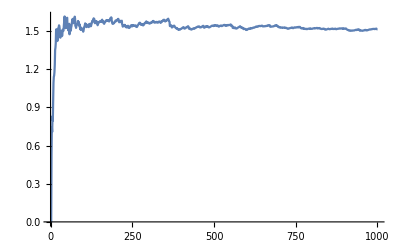

```mathematica
throughputSW=ThroughputTx[packetsSW];
ListLinePlot[throughputSW]
```

2. Dibujar la gráfica teórica de throughput máximo en función del factor a, p, tI y ρ. Hacer gráficas variando cada uno de ellos.

```mathematica
ThroughputTeoricoSW[a_,p_,ti_]:=(1-p)/(a*ti)
```

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Plot[ThroughputTeoricoSW[a,p,ti], {a,1,20}],{p, 0,1}, {ti,0.01,1 }]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Plot[ThroughputTeoricoSW[a,p,ti], {p,0,1}],{a, 1,20}, {ti,0.01,1}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Plot[ThroughputTeoricoSW[a,p,ti], {ti,0.0001,1}],{p, 0,1}, {a,1,20 }]
```

Variación del throughput maximo teórico en función de ρ

En este caso se ha de tener en cuenta que ti=1/mu y que ρ=lamda/mu, por lo que ti=ro/lamda

```mathematica
Manipulate[Plot[ThroughputTeoricoSW[a,p,ro/λ], {ro,0,1}],{p, 0,1}, {a,1,20 }, {λ,1,50}]
```

3.  Calcular el punto de trabajo en esas gráficas para una combinación cualesquiera de esos parámetros y ver cuánto se aproximan a los valores teóricos, supuestas muestras de 1000, 2000 o 5000 segundos.

En este apartado se va a comparar cuanto se aproxima la simulación al resultado teórico. Asimismo, se va a observar el efecto que tiene variar cada uno de los parámetros en la simulación.

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[ax,Prob,ti], {ax,1,20},AxesLabel->{A, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{a,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}]   ,PlotRange->Full  }     ]] ,{a,1,20},{Prob, 0,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Probx,ti], {Probx,0,1},AxesLabel->{prob, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{Prob,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}]  }     ]] ,{a,1,20},{Prob, 0.0009,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Prob,tix], {tix,0.0001,1},AxesLabel->{Ti, γ}],Graphics[{PointSize[Large],Green,Point[{{ti,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}]  }     ]] ,{a,1,20},{Prob, 0,1},  {  ρ, 1, 0.00000001}, {ti, 0.084, 1},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ρ

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Prob,rox/λ], {rox,0.0001,1},AxesLabel->{ro, γ}],Graphics[{PointSize[Large],Green,Point[{{ ρ,Last[ThroughputTx[SimTxSW[λ,λ/ρ,Paquetes,(ρ/λ)*(a-1)/2, 0,Prob]]]}}]  }     ]] ,{a,10,20},{Prob, 0,1},  {  ρ, 0.1,1},{λ, 1,10},{Paquetes, {100,1000,2000,5000}}]
```

Tal y como se puede observar, independientemente del parámetro que se esté variando, la simulación se aproxima bastante al valor teórico por lo que se deduce que la implementación del Stop & Wait se ha realizado de manera correcta.

4. Dibujar los resultados supuesta la aplicación de las abstracciones de rendimiento en una cola M/M/1 supuestas tasas corregidas

El protocolo Stop & Wait se puede simular mediante una cola M/M/1. Para ello, basta con establecer como mu el throughput máximo teórico del protocolo Stop & Wait. A continuación, se contrasta el throughput teórico con el throughput obtenido de simular el protocolo y con el throughput obtenido de utilizar una cola M/M/1 con tasas corregidas.

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[ax,Prob,ti], {ax,1,20},AxesLabel->{A, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{a,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}] ,Blue,Point[{{a,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/(a*ti),Paquetes,ti*(a-1)/2, 0]]]}}]  ,PlotRange->Full  }     ]] ,{a,1,20},{Prob, 0,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Probx,ti], {Probx,0,1},AxesLabel->{prob, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{Prob,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}]  ,Blue,Point[{{Prob,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/(a*ti),Paquetes,ti*(a-1)/2, 0]]]}}]}     ]] ,{a,1,20},{Prob, 0.0009,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Prob,tix], {tix,0.0001,1},AxesLabel->{Ti, γ}],Graphics[{PointSize[Large],Green,Point[{{ti,Last[ThroughputTx[SimTxSW[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,Prob]]]}}]  ,Blue,Point[{{ti,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/(a*ti),Paquetes,ti*(a-1)/2, 0]]]}}]}     ]] ,{a,1,20},{Prob, 0,1},  {  ρ, 1, 0.00000001}, {ti, 0.084, 1},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ρ

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoSW[a,Prob,rox/λ], {rox,0.0001,1},AxesLabel->{ro, γ}],Graphics[{PointSize[Large],Green,Point[{{ ρ,Last[ThroughputTx[SimTxSW[λ,λ/ρ,Paquetes,(ρ/λ)*(a-1)/2, 0,Prob]]]}}]  ,Blue,Point[{{ρ,Last[ThroughputTx[SimTxMM1[λ,(1-Prob)/(a*(ρ/λ)),Paquetes,(ρ/λ)*(a-1)/2, 0]]]}}]}     ]] ,{a,10,30},{Prob, 0,1},  {  ρ, 0.1,1},{λ, 1,10},{Paquetes, {100,1000,2000,5000}}]
```

El resultado en cualquiera de los dos casos simulados se aproxima bastante al valor teórico.

## Parte tercera

1. Resolver la simulación para GO-BACK-N. Inicialmente se puede hacer la simplificación de no considerar las transmisiones dentro de la ventana con de error en la trama. El modulo tiene que ser 8 y ventana infinita. Posteriormente completar la simulación considerando la transmisión de las tramas dentro de la ventana con error y sucesivas.

A diferencia de Stop & Wait, en GO - BACK - N se posee una ventana que permite enviar cierta cantidad de paquetes tan pronto como se pueda, hasta llenar la ventana. Cada vez que se reciba la confirmación del primer paquete de la ventana esta se desplazará, dejando un hueco libre y permitiendo que se envíe un nuevo paquete. Si por el contrario no se recibe la confirmación del primer paquete, se reenviará dicho paquete y todos los paquetes que había en la ventana.

En este caso, la ventana es de 8 paquetes. Los primeros 8 paquetes se enviarán como si estuviéramos en una cola M/M/1, el resto, seguirán la lógica hasta ahora explicada. Si la ventana tiene algún slot libre se enviará el nuevo paquete, sino este tendrá que esperar.

```mathematica
(*GBN[arrivalsTime_, serviceTime_,tprop_, ts_, prob_, N_]:=
Module[{i,firstInWin,nSec, insertionTime,packet, packetList, windowPackets},
i=1;
nSec=0;
insertionTime=0;
firstInWin=1;
packetList={};
windowPackets={};
Map[
(
If[# > insertionTime, insertionTime=#; ]; 
While[Length[windowPackets] > 0 &&insertionTime≥ (windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts)  ,

windowPackets=Drop[windowPackets,1];];
If[Length[windowPackets] ≥ N,
If[insertionTime <(windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts),
 insertionTime=windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts; ];
];

packet={insertionTime,9600* serviceTime[[i]],nSec++,0,0};
AppendTo[windowPackets, packet];
AppendTo[packetList, packet];
insertionTime+=serviceTime[[i++]];

)&,arrivalsTime];
Return[packetList]
]*)

GBN[arrivalsTime_, serviceTime_,tprop_, ts_, prob_, N_, nPacketsTotal_]:=
Module[{i,j,firstInWin,nSec, insertionTime,packet, packetList, windowPackets},
i=1;
j=1;
nSec=0;
insertionTime=0;
firstInWin=1;
packetList={};
windowPackets={};
Map[
(
If[Length[packetList]< nPacketsTotal,
If[# > insertionTime, insertionTime=#; ]; 
While[Length[windowPackets] > 0 &&insertionTime≥ (windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts)  ,

If[windowPackets[[1]][[4]]==1,
If[windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts ≥ windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600,
windowPackets[[1]][[1]]=windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts;,
windowPackets[[1]][[1]]=windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600;];


If[RandomReal[] < prob,windowPackets[[1]][[4]]=1;, windowPackets[[1]][[4]]=0;];
For[j=2,j≤ Length[windowPackets],j++,
windowPackets[[j]][[1]]=windowPackets[[j-1]][[1]]+windowPackets[[j-1]][[2]]/9600;
If[RandomReal[] < prob,windowPackets[[j]][[4]]=1;, windowPackets[[j]][[4]]=0;];
];
packetList=Join[packetList, windowPackets];
,
windowPackets=Drop[windowPackets,1];];];

If[Length[windowPackets] > 0,
If[insertionTime < windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600, insertionTime=windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600;];];


If[Length[windowPackets] ≥ N,
If[insertionTime <(windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts),
While[windowPackets[[1]][[4]]==1,
If[windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts ≥ windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600,
windowPackets[[1]][[1]]=windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts;,
windowPackets[[1]][[1]]=windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600;];


If[RandomReal[] < prob,windowPackets[[1]][[4]]=1;, windowPackets[[1]][[4]]=0;];
For[j=2,j≤ Length[windowPackets],j++,
windowPackets[[j]][[1]]=windowPackets[[j-1]][[1]]+windowPackets[[j-1]][[2]]/9600;
If[RandomReal[] < prob,windowPackets[[j]][[4]]=1;, windowPackets[[j]][[4]]=0;];
];
packetList=Join[packetList, windowPackets];];
If[windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts ≥ windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600,
 insertionTime=windowPackets[[1]][[1]]+windowPackets[[1]][[2]]/9600+2*tprop+ts; ,
insertionTime=windowPackets[[-1]][[1]]+windowPackets[[-1]][[2]]/9600;
];];
];

If[RandomReal[] < prob,
packet={insertionTime,9600* serviceTime[[i]],nSec++,1,0};,
packet={insertionTime,9600* serviceTime[[i]],nSec++,0,0};];

AppendTo[windowPackets, packet];
AppendTo[packetList, packet];
insertionTime+=serviceTime[[i++]];];

)&,arrivalsTime];
Return[packetList]
]

SimTxGBN[lamdaGBN_,muGBN_,nPacketsGBN_,tpropGBN_,tsGBN_,moduloN_,p_]:=Module[

{arrivalsTimeGBN, serviceTimeGBN,packetsGBN},
(
arrivalsTimeGBN=Accumulate[Table[RandomExp[lamdaGBN],nPacketsGBN]];
serviceTimeGBN=Table[RandomExp[muGBN], nPacketsGBN];
SetIniParDraw[tpropGBN,tsGBN];
packetsGBN=GBN[arrivalsTimeGBN, serviceTimeGBN,tpropGBN, tsGBN, p,moduloN, nPacketsGBN];
Return[packetsGBN]
)];
```

```mathematica
muGBN=100;
lamdaGBN=200;
nPacketsGBN=1000;
tpropGBN=0.1;
tsGBN=0.001;
errorProbGBN=0.1;
moduloN=8;

packetsGBN=SimTxGBN[lamdaGBN,muGBN,nPacketsGBN,tpropGBN,tsGBN,moduloN,errorProbGBN];

Manipulate[Show[DrawWin[origin,ww,8],Map[DrawPacketTx[#]&,packetsGBN]],{origin,0,packetsGBN[[-1]][[1]]+2*tpropGBN+tsGBN-ww},{ww,0.1,1}]
```

## Parte cuarta

En este apartado, al igual que en el protocolo Stop & Wait se pretende comparar el throughput teórico con el throughput obtenido de la simulación implementada y de la simulación del protocolo mediante la cola M/M/1. Tal y como se observará en las gráficas posteriores, el resultado de la simulación se asemeja bastante al esperado por lo que la implementación se puede dar como correcta.

1. Dibujar las gráficas teóricas de evolución del throughput máximo en función de  a, p, tI y ρ.

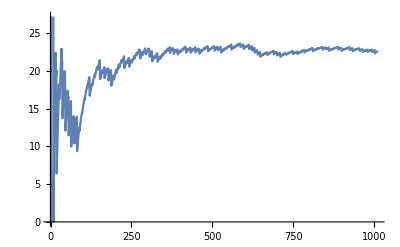

```mathematica
throughputGBN=ThroughputTx[packetsGBN];
ListLinePlot[throughputGBN]
```

```mathematica
ThroughputTeoricoGBN[a_,p_,ti_]:=(1-p)/((1+(a-1)*p)*ti)
```

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Plot[ThroughputTeoricoGBN[a,p,ti], {a,1,20}],{p, 0.1,1}, {ti,0.01,1 }]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Plot[ThroughputTeoricoGBN[a,p,ti], {p,0,1}],{a, 3,20}, {ti,0.01,1}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Plot[ThroughputTeoricoGBN[a,p,ti], {ti,0.0001,1}],{p, 0.1,1}, {a,1,20 }]
```

Variación del throughput maximo teórico en función de ρ

```mathematica
Manipulate[Plot[ThroughputTeoricoGBN[a,p,ro/λ], {ro,0,1}],{p, 0.1,1}, {a,1,20 }, {λ,1,50}]
```

2. Dibujar los resultados experimentales supuesta la simulación de los protocolos

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[ax,Prob,ti], {ax,1,20},AxesLabel->{A, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{a,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}]   ,PlotRange->Full  }     ]] ,{a,1,20},{Prob, 0.1,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Probx,ti], {Probx,0,1},AxesLabel->{prob, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{Prob,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}]  }     ]] ,{a,1,20},{Prob, 0.0009,1},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Prob,tix], {tix,0.0001,1},AxesLabel->{Ti, γ}],Graphics[{PointSize[Large],Green,Point[{{ti,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}]  }     ]] ,{a,1,20},{Prob, 0,1},  {  ρ, 1, 0.00000001}, {ti, 0.084, 1},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ρ

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Prob,rox/λ], {rox,0.0001,1},AxesLabel->{ro, γ}],Graphics[{PointSize[Large],Green,Point[{{ ρ,Last[ThroughputTx[SimTxGBN[λ,λ/ρ,Paquetes,(ρ/λ)*(a-1)/2, 0,8,Prob]]]}}]  }     ]] ,{a,70,200},{Prob, 0.2,0.9999},  {  ρ, 0.1,1},{λ, 0.1,10},{Paquetes, {100,1000,2000,5000}}]
```

3. Dibujar los resultados supuesta la aplicación de las abstracciones de rendimiento en una cola M/M/1 supuestas tasas corregidas

Variación del throughput maximo teórico en función de a

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[ax,Prob,ti], {ax,1,20},AxesLabel->{A, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{a,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}]  ,Blue,Point[{{a,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/((1+(a-1)*Prob)*ti),Paquetes,ti*(a-1)/2, 0]]]}}] ,PlotRange->Full  }     ]] ,{a,1,20},{Prob, 0.1,0.9999},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de p

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Probx,ti], {Probx,0,1},AxesLabel->{prob, γ}, PlotRange->All],Graphics[{PointSize[Large],Green,Point[{{Prob,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}] ,Blue,Point[{{Prob,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/((1+(a-1)*Prob)*ti),Paquetes,ti*(a-1)/2, 0]]]}}] }     ]] ,{a,1,20},{Prob, 0.0009,0.999999},  {  ρ, 1, 0.00000001}, {ti, 0.1, 0.0001},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ti

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Prob,tix], {tix,0.0001,1},AxesLabel->{Ti, γ}],Graphics[{PointSize[Large],Green,Point[{{ti,Last[ThroughputTx[SimTxGBN[ρ/ti,1/ti,Paquetes,ti*(a-1)/2, 0,8,Prob]]]}}]  ,Blue,Point[{{ti,Last[ThroughputTx[SimTxMM1[ρ/ti,(1-Prob)/((1+(a-1)*Prob)*ti),Paquetes,ti*(a-1)/2, 0]]]}}]}     ]] ,{a,1,20},{Prob, 0,0.9999},  {  ρ, 1, 0.00000001}, {ti, 0.084, 1},{Paquetes, {100,1000,2000,5000}}]
```

Variación del throughput maximo teórico en función de ρ

```mathematica
Manipulate[Show[Plot[ThroughputTeoricoGBN[a,Prob,rox/λ], {rox,0.0001,1},AxesLabel->{ro, γ}],Graphics[{PointSize[Large],Green,Point[{{ ρ,Last[ThroughputTx[SimTxGBN[λ,λ/ρ,Paquetes,(ρ/λ)*(a-1)/2, 0,8,Prob]]]}}]  ,Blue,Point[{{ρ,Last[ThroughputTx[SimTxMM1[λ,(1-Prob)/((1+(a-1)*Prob)*(ρ/λ)),Paquetes,(ρ/λ)*(a-1)/2, 0]]]}}]}     ]] ,{a,70,200},{Prob, 0.2,0.9999},  {  ρ, 0.1,1},{λ, 0.1,10},{Paquetes, {100,1000,2000,5000}}]
```